```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
```

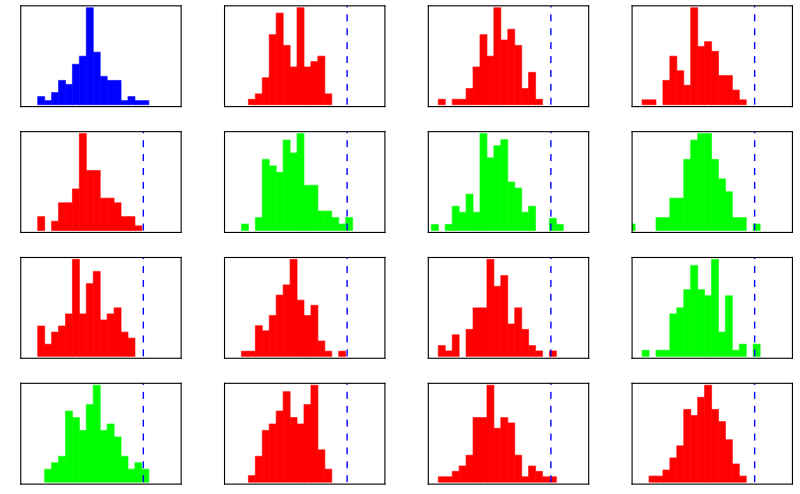

```mathematica
{μ,σ,ν} = {10,2,4};
data = RandomVariate[TruncatedDistribution[{0,∞},StudentTDistribution[μ,σ,ν]],{100}];
{a1,b1}={FindDistributionParameters[data,NormalDistribution[a,b]][[1,2]],FindDistributionParameters[data,NormalDistribution[a,b]][[2,2]]};
gActual =Show[Histogram[data,{1},"Probability",PlotRange->{{0,Max@data+5},Automatic},ChartStyle->Blue,Frame->{True,False,False,False},FrameTicks->{None,None}],Axes->{True,False}];
fRandomPlotter[a_,b_,data__]:=Module[{dataFake=RandomVariate[NormalDistribution[a,b],{100}],aColour},aColour=If[Max@dataFake >Max@data,Green,Red];Histogram[dataFake,{1},"Probability",PlotRange->{{0,Max@data+5},Automatic},ChartStyle->aColour,Frame->{True,False,False,False},FrameTicks->{None,None},Axes->{True,False},Epilog->{Blue,Dashed,Line[{{Max@data,0},{Max@data,10}}]}]]
gFinal=Show[GraphicsGrid[{{gActual,fRandomPlotter[a1,b1,data],fRandomPlotter[a1,b1,data],fRandomPlotter[a1,b1,data]},{fRandomPlotter[a1,b1,data],fRandomPlotter[a1,b1,data],fRandomPlotter[a1,b1,data],fRandomPlotter[a1,b1,data]},{fRandomPlotter[a1,b1,data],fRandomPlotter[a1,b1,data],fRandomPlotter[a1,b1,data],fRandomPlotter[a1,b1,data]},{fRandomPlotter[a1,b1,data],fRandomPlotter[a1,b1,data],fRandomPlotter[a1,b1,data],fRandomPlotter[a1,b1,data]}}],ImageSize->800]
```

```mathematica
Export["Evaluation_amazonExample.pdf",gFinal]
```

Evaluation_amazonExample.pdf

```mathematica
Histogram[
```